### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_Integer,i_Integer]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ϕ[l_List,i_List]:=Product[ϕ[l[[d]],i[[d]]][#[[d]]],{d,1,Length[l]}]&
ψ[l_,i_]:=ϕ[2^l(#1-2^-l i)]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ψ[l_List,i_List]:=Product[ϕ[2^l[[d]](#[[d]]-2^(-l[[d]])i[[d]])],{d,1,Length[l]}]&

proj[f_,x_]:=f[Join[#,{x}]]&

ceil[x_,l_Integer]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
ceil[x_List,l_List]:=Table[If[x[[i]]≥1,2^(l[[i]]-1),1+Floor[2^(l[[i]]-1)x[[i]]]],{i,1,Length[x]}]

atPosition[x_List,l_List,i_List]:=Module[{j,prod,xpos},xpos=ceil[x,l];
											prod=Product[If[xpos[[j]]==i[[j]] || l[[j]]<1,1,0],{j,1,Length[x]}];
											If[prod==1,Return[True];,Return[False];];]
(*Perhaps this could be made more efficient*)

switch[x_]:=If[x≥1,x,1]
switch2[x_]:=If[x==-1,0,If[x==0,1,2^-x]]
switch3[x_,i_]:=If[x≤0,1,(-1)^(i+1)2^-x]

area[kx_]:=Which[kx==-1,1,kx==0,1/2,kx>0,2^-kx]

column2[diag_,row_]:=If[diag<1,diag, If[row<1,diag,diag-row+1]]
column1[diag_,row_]:=If[diag==row,-1,column2[diag,row]]

getrow[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[perp,0],perp≤diag,perp,True,diag]
getcol[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[diag-perp,0],perp> 0,diag-perp,True,diag]

endperp[n_]:=Which[n==-1,-1,n==0,1,True,n+1]

dϕ[x_]:=Which[Abs[x]>1,0,
			x==1 ,-1/2,
			x==-1,1/2,
			x==0,0,
			x>0,-1,
			True,1](* Don't think I need this*)
```

### Standard Lagrange Basis

```mathematica
standardCoefficients[f_,l_List]:=If[Length[l]==1,Table[f[{j 2^(-l[[1]])}],{j,0,2^l[[1]]}],Table[standardCoefficients[proj[f,j 2^(-l[[-1]])],l[[;;-2]]],{j,0,2^l[[-1]]}]]
(*Working*)

standardReconstruct[coefficients_,l_List,x_List]:=If[Length[l]==1,Sum[
coefficients[[i+1]]  ψ[l[[1]],i] [x[[1]]],{i,0,2^l[[1]]}],
Sum[standardReconstruct[coefficients[[i+1]],l[[;;-2]],x[[;;-2]]] ψ[l[[-1]],i] [x[[-1]]],{i,0,2^l[[1]]}]
]
(*The hierarchical and sparse basis will be more efficient*)


standardProject[f_,l_List,x_]:=Module[{},coeffs=standardCoefficients[f,l];Return[standardReconstruct[coeffs,l,x]];]
```

```mathematica
newTimes=Table[Timing[Plot[standardReconstruct[#,{n},{x}],{x,0,1}]&@standardCoefficients[Sin[Pi #[[1]]]&,{n}]][[1]],{n,1,10}]
```

{0.105385,0.020392,0.031387,0.063284,0.098304,0.178179,0.37353,1.16283,2.14766,4.72274}

### Hierarchical Iteration in n-D

```mathematica
hierIterate[l_List,ki_List]:=Module[{k,i,hashEntry,hashMap},hashMap={};If[Length[l]==1,For[k=-1,k≤l[[1]],k++,For[i=1,i≤2^(switch[k]-1),i++,hashEntry={Append[Append[ki,k+2],i]};
hashMap=Join[hashMap,hashEntry];]];Return[hashMap];
,
For[k=-1,k≤l[[1]],k++,
For[i=1,i≤2^(switch[k]-1),i++,hashEntry=hierIterate[l[[2;;]],Append[Append[ki,k+2],i]];hashMap=Join[hashMap,hashEntry]]];Return[hashMap];
]]
(*This is working*)

hierIterate[l_List]:=hierIterate[l,{}]
(*This is working*)
```

### Getting Hierarchical Coefficients

```mathematica
getCoefficient[f_,x_List,l_List]:=If[Length[l]==1,Which[l[[1]]==-1,f[{0}],l[[1]]==0,f[{1}]-f[{0}],True,f[x]-1/2 f[x+2^-l[[1]]]-1/2 f[x-2^-l[[1]]]],
				Which[l[[-1]]==-1,getCoefficient[proj[f,0],x[[;;-2]],l[[;;-2]]],
					l[[-1]]==0,getCoefficient[proj[f,1],x[[;;-2]],l[[;;-2]]]-getCoefficient[proj[f,0],x[[;;-2]],l[[;;-2]]],
					True,getCoefficient[proj[f,x[[-1]]],x[[;;-2]],l[[;;-2]]]-1/2 getCoefficient[proj[f,x[[-1]]+2^(-l[[-1]])],x[[;;-2]],l[[;;-2]]]-1/2getCoefficient[proj[f,x[[-1]]-2^(-l[[-1]])],x[[;;-2]],l[[;;-2]]]
				]
]

pointIndex[x_Real,l_Integer]:=Module[{},Table[If[k≤1,1,ceil[x,k]],{k,-1,l}]]
pointIndex[x_List,l_List]:=Table[pointIndex[x[[i]],l[[i]]],{i,1,Length[l]}]
```

### Full Basis

```mathematica
fullCoefficients[f_,l_List]:=Module[{li,x,i,k,diff,hash},li=hierIterate[l];hash={};For[i=1,i≤Length[li],i++,k=li[[i]][[1;;;;2]]-2;x=2^-k(2li[[i]][[2;;;;2]]-1);
diff=getCoefficient[f,x,k];
(*Print[k,x,diff//N];*)
hash=Join[hash,{li[[i]]-> diff}]];
Return[SparseArray[hash]];
]
(*This is working*)

fullReconstruct[li_,x_,l_]:=Module[{a,k,value,i,d,indices,ki},value=0;d=Length[x]; indices=pointIndex[x,l];
Do[ki=Flatten[Table[{k[a]+2,indices⟦a,k[a]+2⟧},{a,1,d}]];
value+=(li⟦##⟧&@@Sequence[ki])ϕ[ki⟦1;;;;2⟧-2,ki⟦2;;;;2⟧][x],##]&@@Sequence[Table[{k[i],-1,l⟦i⟧},{i,1,d}]];
Return[value];
]

fullReconstruct[li_,x_]:=Module[{a,k,value,i},value=0;
For[a=1,a≤ Length[li],a++,
k=Keys[li[[a]]][[1;;;;2]];
i=Keys[li[[a]]][[2;;;;2]];
If[atPosition[x,k-2,1/2 (i+1)],
value+=Values[li[[a]]] ϕ[k-2,1/2 (i+1)][x]]
];Return[value];]
(*This is working, but you can make it more efficient*)
```

```mathematica
pointIndex[.3,5]
```

{1,1,1,1,2,3,5}

```mathematica
SparseArray[fullCoefficients[Sin[Pi #[[1]]]&,{3}]]
```

SparseArray[<7>, {5, 7}]

```mathematica
fullReconstruct[ArrayRules[fullCoefficients[Sin[Pi #[[1]]]&,{3}]],{.3}]
```

0.793816

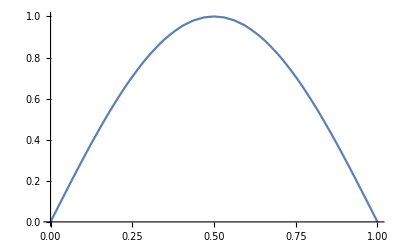

```mathematica
Plot[fullReconstruct[fullCoefficients[Sin[Pi #[[1]]]&,{5}],{x},{5}],{x,0,1}]
```

```mathematica
Plot3D[{Sin[Pi x + y],fullReconstruct[#,{x,y}]},{x,0,1},{y,0,1}]&[fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{3,3}]]
```

-Graphics3D-

### Sparse Iteration in n-D

```mathematica
sparseIterate[n_,d_,ki_List]:=Module[{k,i,hashEntry,hashMap},hashMap={};If[d==1,For[k=-1,k≤n,k++,For[i=1,i≤2^switch[k]-1,i+=2,hashEntry={Append[Append[ki,k+2],i]};
hashMap=Join[hashMap,hashEntry];]];Return[hashMap];
,
For[k=-1,k≤n,k++,
For[i=1,i≤2^switch[k]-1,i+=2,hashEntry=sparseIterate[n-k-1,d-1,Append[Append[ki,k+2],i]];hashMap=Join[hashMap,hashEntry]]];Return[hashMap];
]]
(*This is working*)

sparseIterate[n_,d_]:=sparseIterate[n,d,{}]
(*This is working*)
```

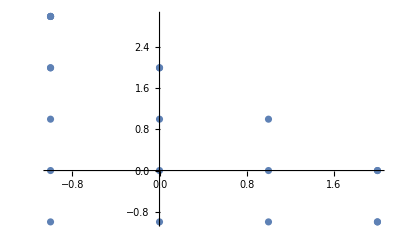

```mathematica
sparseIterate[2,2][[;;,1;;;;2]]//ListPlot
```

```mathematica
Plot3D[{fullReconstruct[#,{x,y}]-Sin[Pi x+ y]},{x,0,1},{y,0,1},PlotRange->Full]&@sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,5,2]
```

-Graphics3D-

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j,getrow[perp,diag],getcol[perp,diag]],{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]


sparseCoefficients[f_,n_,d_]:=Module[{li,hash,k,i,diff,x},li=sparseIterate[n,d];
hash={};
For[i=1,i≤Length[li],i++,k=li[[i]][[1;;;;2]]-2;x=2^-k li[[i]][[2;;;;2]];
diff=getCoefficient[f,x,k];
hash=Join[hash,{li[[i]]-> diff}];];
Return[hash];
]



sparseReconstruct2D[coefficients_]:=Sum[Sum[coefficients[[diag+2,perp+2,ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]]] 
ϕ[getrow[perp,diag],getcol[perp,diag],ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]][#1,#2]
,{perp,-1,endperp[diag]}],{diag,-1,Length[coefficients]-2}]&


sparseReconstruct[coefficients_]:=fullReconstruct[coefficients]

sparseProject2D[f_,n_]:=sparseReconstruct2D[sparseCoefficients2D[f,n]]


reverseFlattenSparse[coefficients_,n_]:=Module[{k},k=0;Return[Table[Table[Table[coefficients⟦++k⟧ ,{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]];]
```

### Differentiation

```mathematica
diffx[f_,l_Integer,x_List]:=Module[{ans,temp},temp=x;Which[x⟦1⟧< 2^-l,temp⟦1⟧+=2^-l; ans=f[temp]-f[x]; ans*=2^l;,
x⟦1⟧>1-2^-l ,temp⟦1⟧-=2^-l; ans=f[x]-f[temp]; ans*=2^l;,
True,temp⟦1⟧+=2^-l;ans=f[temp];temp⟦1⟧-=2 2^-l; ans-=f[temp];ans*=(2^(l-1));];Return[ans];]
(*This is working.. I think it's efficient. We could do a general one: *)

diff[f_,l_Integer,x_List,i_:1]:=Module[{ans,temp},temp=x;Which[x⟦i⟧< 2^-l,temp⟦i⟧+=2^-l; ans=f[temp]-f[x]; ans*=2^l;,
x⟦i⟧>1-2^-l ,temp⟦i⟧-=2^-l; ans=f[x]-f[temp]; ans*=2^l;,
True,temp⟦i⟧+=2^-l;ans=f[temp];temp⟦i⟧-=2 2^-l; ans-=f[temp];ans*=(2^(l-1));];Return[ans];]

(*And just in case:*)
grad[f_,l_List,x_List]:=Table[diff[f,l[[i]],x,i],{i,1,Length[x]}]
```

```mathematica
(*Past this point idk... *)
```

### Algorithms to form the D Matrices

```mathematica
dxMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffx[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]//Transpose
dyMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffy[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]//Transpose


dxMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffx[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]
dyMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffy[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]


dxMatrixSparse[n_]:=Flatten[Table[Table[Table[
sparseCoefficients2D[diffx[ϕ[getrow[perp,diag],getcol[perp,diag],i,j],n],n]//Flatten,{i,1,2^(switch[getrow[perp,diag]]-1)},{j,1,2^(switch[getcol[perp,diag]]-1)}],{perp,-1,endperp[diag]}],{diag,-1,n}],3]//Transpose

dyMatrixSparse[n_]:=Flatten[Table[Table[Table[
sparseCoefficients2D[diffy[ϕ[getrow[perp,diag],getcol[perp,diag],i,j],n],n]//Flatten,{i,1,2^(switch[getrow[perp,diag]]-1)},{j,1,2^(switch[getcol[perp,diag]]-1)}],{perp,-1,endperp[diag]}],{diag,-1,n}],3]//Transpose
```

### Showing the Grids

```mathematica
makeFull[lx_,ly_]:=Table[Table[{switch2[kx] i,switch2[ky] j},{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]
```

```mathematica
makeSparse[n_]:=Table[Table[Table[{switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j},{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```

### Integration on the Grids

```mathematica
posW[x_]:=If[(x==0||x==1),1/2,1]


fullIntegrate[f_,kx_,ky_]:=Sum[2^-kx 2^-ky  posW[i]posW[j] f[i,j],{i,0,1,2^-kx},{j,0,1,2^-ky}]

fullIntegrate[f_,kx_]:=Sum[2^-kx  posW[i]f[i],{i,0,1,2^-kx}]

sparseIntegrate[f_,n_]:=Sum[Sum[Sum[posW[switch2[getrow[perp,diag]] i]posW[switch2[getcol[perp,diag]] j]switch2[getcol[perp,diag]]switch2[n]f[switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j],{i,1,2^switch[getrow[perp,diag]],2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]

sparseIntegrateByCoefficients[f_,n_]:=Sum[Sum[Sum[getCoefficient2D[f,switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j,getrow[perp,diag],getcol[perp,diag]] area[getrow[perp,diag]] area[getcol[perp,diag]],{i,1,2^switch[getrow[perp,diag]],2},{j,1,2^switch[getcol[perp,diag]],2}]
,{perp,-1,endperp[diag]}],{diag,-1,n}]


sparseBoundaryXIntegrate[f_,n_]:=0 (*do later, if you find a better definition*)

(*Sum[Sum[posW[i]posW[j] 1/GCD[2^n i,2^(n)] 1/2^n f[i, j ],{j,0,1,1/GCD[2^n i,2^(n)]}],{i,0,1,2^(-n)}]*)


(*The area weights, although they sum to 1, are not totally right for sparse grids*)
```

### Weights for the Sparse Grid

```mathematica
weights1D[i_,kx_,lx_]:=If[Mod[i,2^(lx-kx)]==0,switch3[kx,2^(kx-lx)i],0]

showFullWeights[lx_,ly_]:=Sum[Table[weights1D[i,kx,lx] weights1D[j,ky,ly],{i,0,2^lx},{j,0,2^ly}],{kx,0,lx},{ky,0,ly}]

showSparseWeights[n_]:=Table[weights1D[i,0,n] weights1D[j,0,n],{i,0,2^n},{j,0,2^n}]+Sum[Sum[Table[weights1D[i,Max[0,getrow[perp,diag]],n]weights1D[j,Max[0,getcol[perp,diag]],n],{i,0,2^n},{j,0,2^n}],{perp,-1,endperp[diag]}],{diag,1,n}]
```

### Algorithms to form the W Matrices

```mathematica
lagrangeW[lx_,ly_]:=Flatten[Table[Table[fullIntegrate[ψ[lx,ly,i1,j1][#1,#2] ψ[lx,ly,i2,j2][#1,#2]&,lx,ly],{i2,0,2^lx},{j2,0,2^ly}]//Flatten,{i1,0,2^lx},{j1,0,2^ly}],1]

lagrangedW[lx_,ly_]:=Flatten[Table[Table[fullIntegrate[ψ[lx,ly,i1,j1][1,#1] ψ[lx,ly,i2,j2][1,#1]-ψ[lx,ly,i1,j1][0,#1] ψ[lx,ly,i2,j2][0,#1]&,ly],{i2,0,2^lx},{j2,0,2^ly}]//Flatten,{i1,0,2^lx},{j1,0,2^ly}],1]

fullW[lx_,ly_]:=Flatten[Table[Table[Table[Table[fullIntegrate[ϕ[kx1,ky1,i1,j1][#1,#2] ϕ[kx2,ky2,i2,j2][#1,#2]&,lx,ly],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}],3]

fulldW[lx_,ly_]:=Flatten[Table[Table[Table[Table[fullIntegrate[ϕ[kx1,ky1,i1,j1][1,#] ϕ[kx2,ky2,i2,j2][1,#]-ϕ[kx1,ky1,i1,j1][0,#] ϕ[kx2,ky2,i2,j2][0,#]&,ly],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}],3]

sparseW[n_]:=Flatten[Table[Table[Table[Table[Table[Table[
sparseIntegrateByCoefficients[ϕ[getrow[perp1,diag1],getcol[perp1,diag1],i1,j1][#1,#2]ϕ[getrow[perp2,diag2],getcol[perp2,diag2],i2,j2][#1,#2]&,n],{i2,1,2^(switch[getrow[perp2,diag2]]-1)},{j2,1,2^(switch[getcol[perp2,diag2]]-1)}],{perp2,-1,endperp[diag2]}],{diag2,-1,n}]//Flatten,{i1,1,2^(switch[getrow[perp1,diag1]]-1)},{j1,1,2^(switch[getcol[perp1,diag1]]-1)}],{perp1,-1,endperp[diag1]}],{diag1,-1,n}],3]

sparsedW[n_]:=Flatten[Table[Table[Table[Table[Table[Table[
sparseBoundaryXIntegrate[ϕ[getrow[perp1,diag1],getcol[perp1,diag1],i1,j1][#1,#2]ϕ[getrow[perp2,diag2],getcol[perp2,diag2],i2,j2][#1,#2]&,n],{i2,1,2^(switch[getrow[perp2,diag2]]-1)},{j2,1,2^(switch[getcol[perp2,diag2]]-1)}],{perp2,-1,endperp[diag2]}],{diag2,-1,n}]//Flatten,{i1,1,2^(switch[getrow[perp1,diag1]]-1)},{j1,1,2^(switch[getcol[perp1,diag1]]-1)}],{perp1,-1,endperp[diag1]}],{diag1,-1,n}],3]
```

### Redefining differentiation (Sparse Differentiation)

```mathematica
sparseDiffx[f_,n_,kx_,ky_,i_,j_]:=Which[#1< 2^-n,(f[#1+2^-l,#2]-f[#1,#2])/2^-l,#1>1-2^-n ,(f[#1,#2]-f[#1-2^-l,#2])/2^-l,True,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]&


sparseDiffy[f_,l_]:=
Which[#2< 2^-l,(f[#1,#2+2^-l]-f[#1,#2])/2^-l,#2> 1-2^-l,(f[#1,#2]-f[#1,#2-2^-l])/2^-l,True,(f[#1,#2+2^-l]-f[#1,#2-2^-l])/(2 2^-l)]&
```